```mathematica
(*81 lines per section*)
(*r Zr-Zr C-Zr C-C Total*)
What are the objective of being able to classify Frenkel pairs?
```

What are the objective of being able to Classify Frenkels?
1) It is hugely time consuming to analyze defect-type in MD trajectories
2) Kinetics: we can estimate the type-lifetimes at different temperatures, and use this as means to estimate diffusion barriers
3) Thermodynamics: probe anharmonicity by comparing relative defect populations at TC to quasi-harmonic defect populations. It

## Classifier for Frenkel pairs

```mathematica
Ideas to improve the classifier:
1) Each volume has its own classifier
2) Difference the PDF with respect to an average perfect run at that temperature
3) Include Zr-C as well as C-C PDF
4) Include a few steps a high tempertures in the training model
```

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/"];
filesTrain={"pdf_OUT_129.4850/pdf.129.4850.300.1_1141.txt","pdf_OUT_142.4850/pdf.142.4850.300.1_891.txt",
"pdf_OUT_70.4850/m.pdf.70.4850.300.1_842.txt","pdf_OUT_174.4850/pdf.174.4850.300.1_851.txt",
"pdf_OUT_1126.4850/pdf.1126.4850.300.1_746.txt","pdf_OUT_perf.4850/m.pdf.PERF.4850.300.1_1071.txt"};


(*files={"pdf.70.4850.1_836.txt","pdf.129.4850.1_1141.txt","pdf.142.4850.1_891.txt","pdf.174.4850.1_851.txt","pdf.1126.4850.1_746.txt","pdf.PERF.4850.1_1071.txt"};*)
pdfData=Table[ReadList[filesTrain[[i]],{Number,Number,Number,Number,Number}],{i,1,6}];

names={"129","142","70","174","1126","PERF"};
temperatures={"300","760","1900","2500","3200","3805"};
fullNames={"Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-trimer","Unbound-tetramer","Perfect"};
header={"Methods","Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-Trimer","Unbound-Tetramer","Perfect"};
(*volumes={"V=V(0.75T_C)","V=V(0.9T_C)"};*)

zrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[2]]},{i,1,6}];
czr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[3]]},{i,1,6}];
cc=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]]},{i,1,6}];
tot=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[5]]},{i,1,6}];
all=Table[Transpose@{Transpose[pdfData[[i]]][[2]],Transpose[pdfData[[i]]][[3]],Transpose[pdfData[[i]]][[4]]},{i,1,6}];
ccczr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]],Transpose[pdfData[[i]]][[3]]},{i,1,6}];
ccczrzrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]],Transpose[pdfData[[i]]][[3]],Transpose[pdfData[[i]]][[2]]},{i,1,6}];

methods={"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","RandomForest","SupportVectorMachine"}
methodsProduction={"LogisticRegression","SupportVectorMachine"}

plotStyleA={PlotRange->All,PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["r (Å)",18,Black],Style["ρ(r, t)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
```

{LogisticRegression,Markov,NaiveBayes,NearestNeighbors,RandomForest,SupportVectorMachine}

{LogisticRegression,SupportVectorMachine}

```mathematica
Table[zrzr[[i]]//Length,{i,1,Length@zrzr}]
```

{18549,14499,13689,13851,12150,17415}

### PDF plots

```mathematica
ListLinePlot[Partition[zrzr[[1]],81],PlotRange->All];
ListLinePlot[Partition[zrzr[[6]],81],PlotRange->All];
```

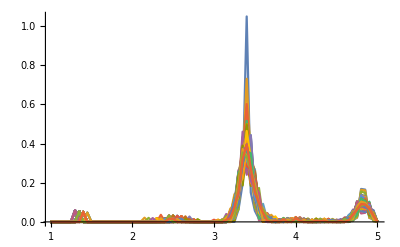
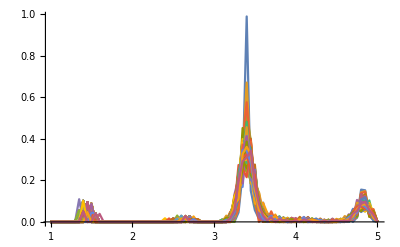
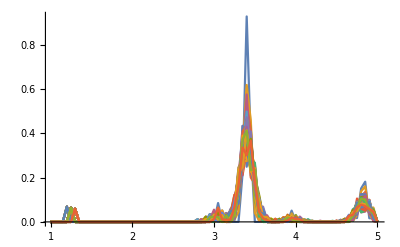
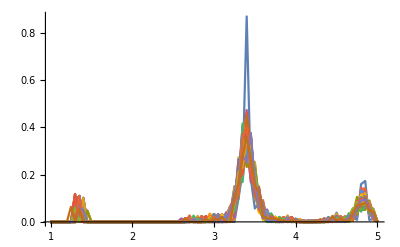
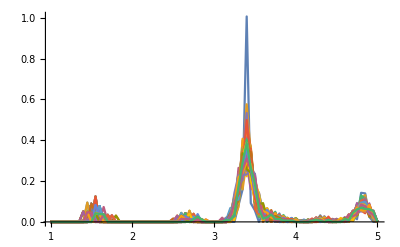

```mathematica
Table[ListLinePlot[Partition[cc[[i]],81],PlotRange->All],{i,1,5}]
```

```mathematica
ListLinePlot[Partition[tot[[1]],81][[1;;10]],PlotRange->All];
```

```mathematica
With[{name=czr},ListAnimate[Table[ListLinePlot[Partition[name[[1]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[1]],81]//Length}],15]];
```

### PDF animations

```mathematica
ccAnimation=Table[With[{name=cc},ListAnimate[Table[ListLinePlot[Partition[name[[j]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,PlotLabel->fullNames[[j]],FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[j]],81]//Length}],25]],{j,1,6}];
```

$Aborted

```mathematica
(*Export["B2-test-data-300K.avi",ccAnimation[[1]],"Animation","AnimationRepetitions"->2,"ControlAppearance"->None]*)
plotStyle={PlotRange->{{0,5},{0,.5}},PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["r (Å)",18,Black],Style["ρ(r)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/animations"];
framesTrainingCC=Table[With[{name=cc},Table[ListLinePlot[Partition[name[[j]],81][[i]],plotStyle,PlotLabel->Style[fullNames[[j]],18,Black]],{i,1,Partition[name[[j]],81]//Length}]],{j,1,6}];
framesTrainingCCJoined=Join[framesTrainingCC[[1]],framesTrainingCC[[2]]];
(*Export["framesTrainingCC.gif",framesTrainingCCJoined,"AnimationRepetitions"->1,"ControlAppearance"->None,"FrameRate"->25]*)
```

```mathematica
With[{name=zrzr},ListAnimate[Table[ListLinePlot[Partition[name,81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name,81]//Length}],15]]
```

ListAnimate[{},15]

```mathematica
With[{name=czr},ListAnimate[Table[ListLinePlot[Partition[name[[1]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[1]],81]//Length}],15]]
```

## Train classifier

```mathematica
Table[Length[cc[[i]]]/81//N,{i,1,Length@cc}]
```

{229.,179.,169.,171.,150.,215.}

```mathematica
Options@Classify
methods={"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","RandomForest","SupportVectorMachine"}
```

{Method→Automatic,PerformanceGoal→Automatic,NominalVariables→Automatic,ValidationSet→None,FeatureNames→Automatic,FeatureTypes→Automatic,IndeterminateThreshold→Automatic,UtilityFunction→Automatic,Weights→Automatic,FeatureWeights→Automatic,DistributionPostProcessing→Automatic,PredictionName→Automatic,RecordLog→True,FeatureExtractor→None,ImputeMissingValues→True,ProcessorCaching→True,BatchProcessing→Automatic,MinimalPreprocessing→False,ClassPriors→Automatic,TieBreakerFunction→RandomChoice}

{LogisticRegression,Markov,NaiveBayes,NearestNeighbors,RandomForest,SupportVectorMachine}

### Standard

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsStandard=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.941176 | 1. | 1. | 0.921569 | 1.
0.647059 | 0.686275 | 0.803922 | 0.686275 | 0.705882 | 0.784314
0.941176 | 0.941176 | 1. | 1. | 0.901961 | 1.
0.529412 | 0.921569 | 0.980392 | 1. | 0.921569 | 1.
0.941176 | 0.941176 | 1. | 1. | 0.823529 | 1.
1. | 0.960784 | 1. | 1. | 0.980392 | 1.

```mathematica
(*trainingSet=50,ValidationSet=100*)
finalResultsStandard//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer | Unbound-Trimer | Unbound-Tetramer | 
LogisticRegression | 0.941176 | 0.941176 | 1. | 1. | 0.921569 | 1.
Markov | 0.647059 | 0.686275 | 0.803922 | 0.686275 | 0.705882 | 0.784314
NaiveBayes | 0.941176 | 0.941176 | 1. | 1. | 0.901961 | 1.
NearestNeighbors | 0.529412 | 0.921569 | 0.980392 | 1. | 0.921569 | 1.
RandomForest | 0.941176 | 0.941176 | 1. | 1. | 0.823529 | 1.
SupportVectorMachine | 1. | 0.960784 | 1. | 1. | 0.980392 | 1.

### Explicit r index for c-c

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsExpl=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.941176 | 1. | 1. | 0.921569 | 1.
0.666667 | 0.666667 | 0.803922 | 0.666667 | 0.705882 | 0.686275
0.941176 | 0.941176 | 1. | 1. | 0.901961 | 1.
0.529412 | 0.921569 | 0.980392 | 1. | 0.921569 | 1.
0.980392 | 0.941176 | 1. | 1. | 1. | 1.
1. | 0.960784 | 1. | 1. | 0.980392 | 1.

### Log

```mathematica
{#[[1]],2#[[2]]}&/@Transpose@{{1,2,3,4},{10,11,12,13}};
funny={#[[1]],#[[2]]-#[[3]]}&;
funny/@Transpose@{{1,2,3,4},{10,11,12,13},{10,11,12,23}};
```

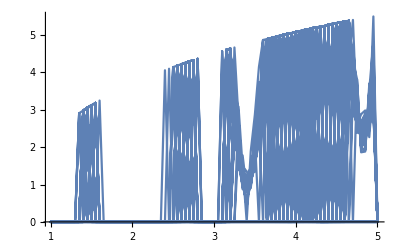

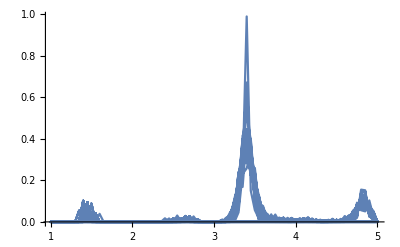

```mathematica
loggy={#[[1]],-Log@#[[2]]/.Indeterminate->0}&;
ListLinePlot[loggy/@cc[[2]][[1;;5000]],PlotRange->All]
ListLinePlot[cc[[2]][[1;;5000]],PlotRange->All]
```

```mathematica
cclog=Table[loggy/@cc[[type]],{type,1,6}];
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cclog[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cclog[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsLog=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.901961 | 0.941176 | 1. | 1. | 0.843137 | 1.
0.588235 | 0.54902 | 0.862745 | 0.666667 | 0.745098 | 0.764706
0.980392 | 0.921569 | 1. | 1. | 0.882353 | 1.
0.588235 | 0.921569 | 1. | 1. | 0.901961 | 1.
0.941176 | 0.901961 | 1. | 0.980392 | 0.764706 | 1.
0.960784 | 0.960784 | 1. | 1. | 0.882353 | 1.

### Joint space c-c and c-zr

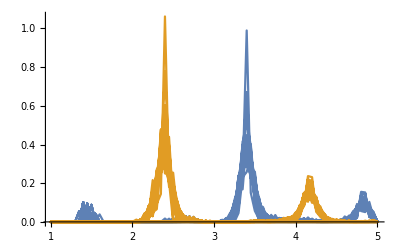

```mathematica
ListLinePlot[{cc[[2]][[1;;5000]],czr[[2]][[1;;5000]]},PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccczr[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccczr[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsJoint=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

1. | 0.921569 | 1. | 1. | 0.921569 | 1.
0.607843 | 0.627451 | 0.705882 | 0.666667 | 0.72549 | 0.980392
0.843137 | 0.980392 | 1. | 1. | 0.941176 | 1.
0.647059 | 0.941176 | 1. | 1. | 0.921569 | 1.
0.921569 | 0.960784 | 1. | 0.980392 | 0.901961 | 1.
1. | 0.960784 | 1. | 1. | 1. | 1.

### Three part joint space - c-c c-zr zr-zr

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccczrzrzr[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccczrzrzr[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsJoint3=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.882353 | 1. | 1. | 0.882353 | 1.
0.627451 | 0.529412 | 0.705882 | 0.745098 | 0.686275 | 0.960784
0.882353 | 0.980392 | 1. | 1. | 0.941176 | 1.
0.764706 | 0.921569 | 1. | 1. | 0.862745 | 1.
0.901961 | 0.980392 | 1. | 1. | 0.803922 | 1.
0.980392 | 0.941176 | 1. | 1. | 0.921569 | 1.

### Sum space for c-c plus c-zr

```mathematica
ccsum;
```

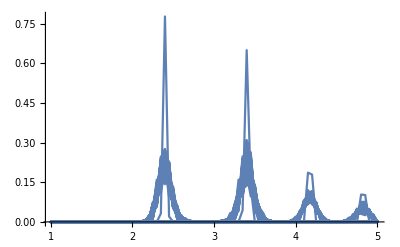

```mathematica
summy={#[[1]],0.5*(#[[2]]+#[[3]])}&;
ccsum=Table[summy/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccsum[[6]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsum[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsum[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.980392 | 0.921569 | 1. | 1. | 0.941176 | 1.
0.627451 | 0.431373 | 0.843137 | 0.568627 | 0.607843 | 0.882353
0.843137 | 0.823529 | 0.960784 | 1. | 0.980392 | 1.
0.960784 | 0.941176 | 1. | 0.980392 | 0.921569 | 1.
0.901961 | 0.941176 | 1. | 1. | 0.980392 | 1.
0.980392 | 0.980392 | 1. | 1. | 1. | 1.

### Sum space for c-c and zr-c, and for c-c and zr-zr

```mathematica
summy4={#[[1]],0.5*(#[[2]]+#[[3]]),0.5*(#[[2]]+#[[4]])}&;
ccsum4=Table[summy4/@ccczrzrzr[[type]],{type,1,6}];
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsum4[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsum4[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum4=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.980392 | 0.960784 | 1. | 1. | 0.901961 | 1.
0.627451 | 0.647059 | 0.843137 | 0.686275 | 0.745098 | 0.980392
0.862745 | 0.960784 | 1. | 1. | 1. | 1.
0.941176 | 0.980392 | 1. | 1. | 0.882353 | 1.
0.980392 | 0.960784 | 1. | 1. | 0.901961 | 1.
0.980392 | 0.980392 | 1. | 1. | 0.980392 | 1.

### Sum space for c-c plus c-zr

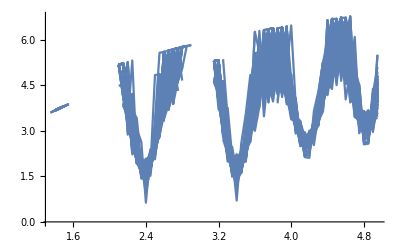

```mathematica
summyL={#[[1]],-Log[0.5*(#[[2]]+#[[3]])]}&;
ccsumL=Table[summyL/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccsumL[[2]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsumL[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsumL[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.235294 | 0.333333 | 0.607843 | 0.784314 | 0.862745 | 0.941176
0.431373 | 0.294118 | 0.509804 | 0.529412 | 0.313725 | 0.882353
0.745098 | 0.666667 | 0.901961 | 0.941176 | 0.901961 | 0.960784
0.137255 | 0.313725 | 0.45098 | 0.588235 | 0.784314 | 0.960784
0.254902 | 0.54902 | 0.509804 | 0.764706 | 0.764706 | 0.921569
0.45098 | 0.568627 | 0.784314 | 0.882353 | 0.823529 | 0.941176

```mathematica
Sum space for c-c plus zr-zr
```

-zr+for space Sum ClassifierFunction[…]-plus zr ClassifierFunction[…]

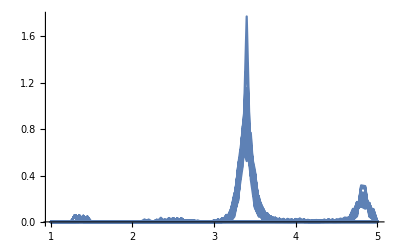

```mathematica
summy2={#[[1]],(#[[2]]+#[[4]])}&;
ccsum2=Table[summy2/@ccczrzrzr[[type]],{type,1,6}];
ListLinePlot[ccsum2[[1]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsum2[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsum2[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum2=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.980392 | 0.980392 | 1. | 1. | 0.921569 | 1.
0.509804 | 0.705882 | 0.784314 | 0.882353 | 0.666667 | 0.882353
0.803922 | 0.960784 | 1. | 1. | 0.980392 | 1.
0.941176 | 0.960784 | 1. | 1. | 0.882353 | 1.
0.921569 | 0.921569 | 1. | 1. | 0.941176 | 1.
0.980392 | 0.980392 | 1. | 1. | 0.980392 | 1.

### Sum space for c-c plus zr-zr plus zr-c

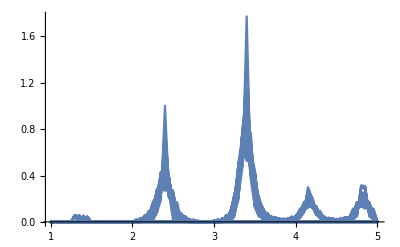

```mathematica
summy3={#[[1]],(#[[2]]+#[[3]]+#[[4]])}&;
ccsum3=Table[summy3/@ccczrzrzr[[type]],{type,1,6}];
ListLinePlot[ccsum3[[1]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsum3[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsum3[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum3=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.921569 | 1. | 1. | 0.941176 | 1.
0.607843 | 0.54902 | 0.686275 | 0.627451 | 0.607843 | 0.921569
0.784314 | 0.823529 | 0.980392 | 0.980392 | 1. | 1.
0.980392 | 0.921569 | 0.980392 | 1. | 0.901961 | 1.
1. | 0.941176 | 1. | 0.980392 | 0.941176 | 1.
0.980392 | 0.960784 | 1. | 1. | 1. | 1.

### Diff c-c minus zr-zr

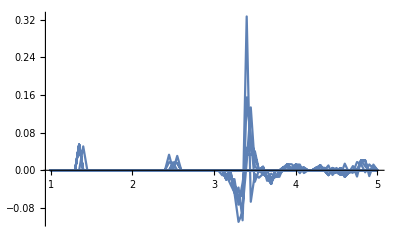

```mathematica
diff2={#[[1]],(#[[2]]-#[[4]])}&;
ccdiff2=Table[diff2/@ccczrzrzr[[type]],{type,1,6}];
ListLinePlot[ccdiff2[[1]][[1;;400]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiff2[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiff2[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiff2=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.862745 | 0.960784 | 1. | 0.980392 | 0.941176 | 1.
0.568627 | 0.666667 | 0.921569 | 0.745098 | 0.705882 | 1.
0.784314 | 0.901961 | 0.960784 | 1. | 0.823529 | 1.
0.45098 | 0.843137 | 1. | 0.882353 | 0.705882 | 1.
0.941176 | 0.980392 | 0.980392 | 1. | 0.921569 | 0.980392
0.901961 | 0.960784 | 1. | 1. | 0.960784 | 1.

### Diff c-c minus c-zr abs

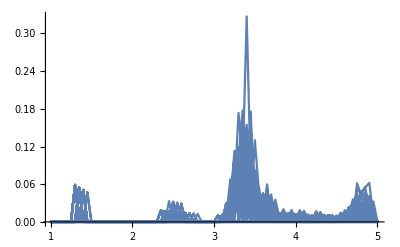

```mathematica
diff3={#[[1]],Abs@(#[[2]]-#[[4]])}&;
ccdiff3=Table[diff3/@ccczrzrzr[[type]],{type,1,6}];
ListLinePlot[ccdiff3[[1]][[1;;4000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiff3[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiff3[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiff3=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.784314 | 0.921569 | 1. | 1. | 0.960784 | 1.
0.470588 | 0.54902 | 0.745098 | 0.647059 | 0.666667 | 0.823529
0.803922 | 0.882353 | 1. | 1. | 0.823529 | 1.
0.352941 | 0.843137 | 0.980392 | 0.882353 | 0.764706 | 1.
0.941176 | 0.882353 | 0.980392 | 1. | 0.960784 | 1.
0.843137 | 0.941176 | 0.960784 | 1. | 0.960784 | 1.

### Diff c-c minus zr-zr and c-c plus zr-c

```mathematica
diffsum={#[[1]],(#[[2]]-#[[4]]),(#[[2]]+#[[3]])}&;
ccdiffsum=Table[diffsum/@ccczrzrzr[[type]],{type,1,6}];
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiffsum[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiffsum[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiffSum=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

$Aborted

### Diff space for c-c minus c-zr

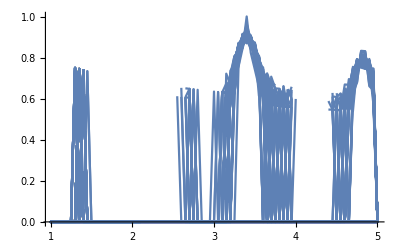

```mathematica
diffy={#[[1]],(#[[2]]-#[[3]])^0.1}&;
ccdiff=Table[diffy/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccdiff[[1]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiff[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiff[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiff=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.882353 | 0.882353 | 1. | 0.941176 | 0.823529 | 1.
0.647059 | 0.529412 | 0.745098 | 0.607843 | 0.705882 | 0.901961
0.705882 | 0.882353 | 0.921569 | 0.980392 | 0.803922 | 1.
0.843137 | 0.921569 | 0.921569 | 0.764706 | 0.784314 | 1.
0.882353 | 0.960784 | 1. | 0.980392 | 0.784314 | 1.
0.921569 | 0.901961 | 1. | 0.941176 | 0.784314 | 1.

### Difference c-c minus zr-zr with absolute

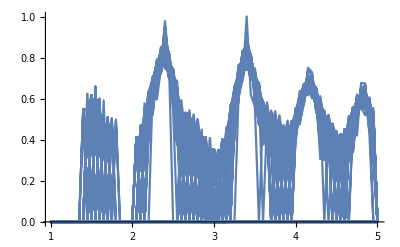

```mathematica
diffyAbs={#[[1]],((#[[2]]-#[[3]])^2)^0.1}&;
ccdiffAbs=Table[diffyAbs/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccdiffAbs[[5]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiffAbs[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiffAbs[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiff=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.921569 | 0.901961 | 0.980392 | 0.901961 | 0.862745 | 1.
0.72549 | 0.647059 | 0.764706 | 0.568627 | 0.588235 | 0.901961
0.784314 | 0.843137 | 0.960784 | 1. | 0.803922 | 1.
0.960784 | 0.921569 | 0.960784 | 0.921569 | 0.901961 | 1.
0.901961 | 0.921569 | 1. | 0.980392 | 0.745098 | 1.
0.921569 | 0.960784 | 0.980392 | 0.921569 | 0.882353 | 1.

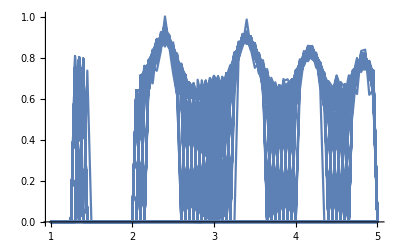

```mathematica
diffyAbs2={#[[1]],Abs[(#[[2]]-#[[3]])]^0.1}&;
ccdiffAbs2=Table[diffyAbs2/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccdiffAbs2[[4]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiffAbs2[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiffAbs2[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiffAbs2=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.882353 | 0.882353 | 0.980392 | 0.901961 | 0.862745 | 1.
0.705882 | 0.588235 | 0.823529 | 0.529412 | 0.588235 | 0.901961
0.784314 | 0.843137 | 0.960784 | 1. | 0.784314 | 1.
0.941176 | 0.941176 | 0.941176 | 0.921569 | 0.843137 | 1.
0.941176 | 0.921569 | 1. | 0.941176 | 0.784314 | 1.
0.901961 | 0.960784 | 0.980392 | 0.921569 | 0.862745 | 1.

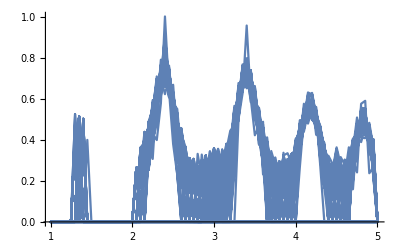

```mathematica
diffyAbs3={#[[1]],Abs[(#[[2]]-#[[3]])]^0.3}&;
ccdiffAbs3=Table[diffyAbs3/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccdiffAbs3[[4]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiffAbs3[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiffAbs3[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiffAbs2=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.882353 | 0.980392 | 0.901961 | 0.862745 | 1.
0.745098 | 0.607843 | 0.823529 | 0.509804 | 0.588235 | 0.901961
0.784314 | 0.843137 | 0.960784 | 1. | 0.803922 | 1.
0.960784 | 0.843137 | 0.980392 | 0.921569 | 0.862745 | 1.
0.901961 | 0.921569 | 1. | 0.941176 | 0.72549 | 1.
0.901961 | 0.960784 | 0.980392 | 0.921569 | 0.901961 | 1.

### All

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[all[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[all[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsAll=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.960784 | 0.882353 | 1. | 1. | 0.901961 | 1.
0.647059 | 0.509804 | 0.72549 | 0.764706 | 0.666667 | 0.980392
0.882353 | 0.980392 | 1. | 1. | 0.941176 | 1.
0.843137 | 0.921569 | 1. | 1. | 0.921569 | 1.
0.980392 | 0.941176 | 1. | 0.980392 | 0.941176 | 1.
0.980392 | 0.941176 | 1. | 1. | 0.921569 | 1.

#### Conclusions

The support vector Machine, and linear logistic regression kernel are both pretty tight. The best results are obtained for c-c + zr-c, so lets use that therefore to train a production linear and support vector vector

```mathematica
plotStyleA={PlotRange->All,PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["r (Å)",18,Black],Style["ρ(r, t)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
```

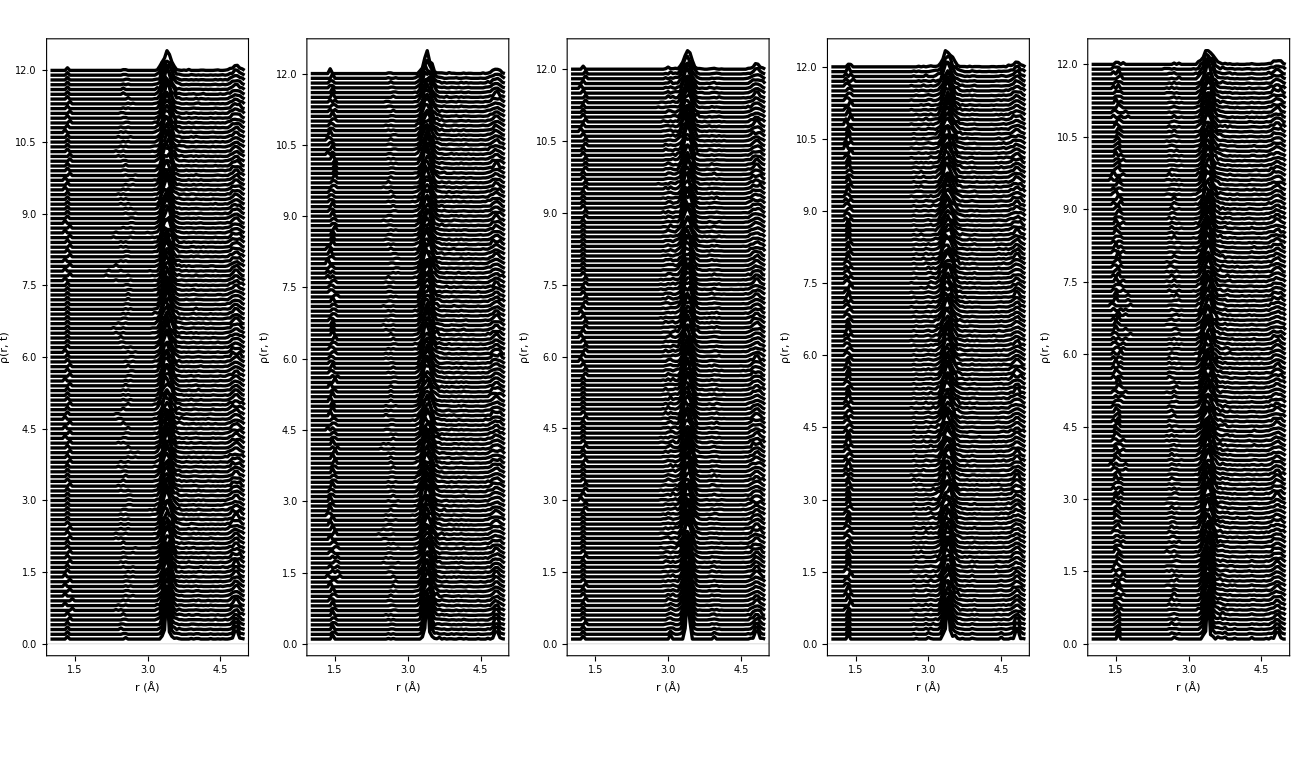

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[cc[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,120}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

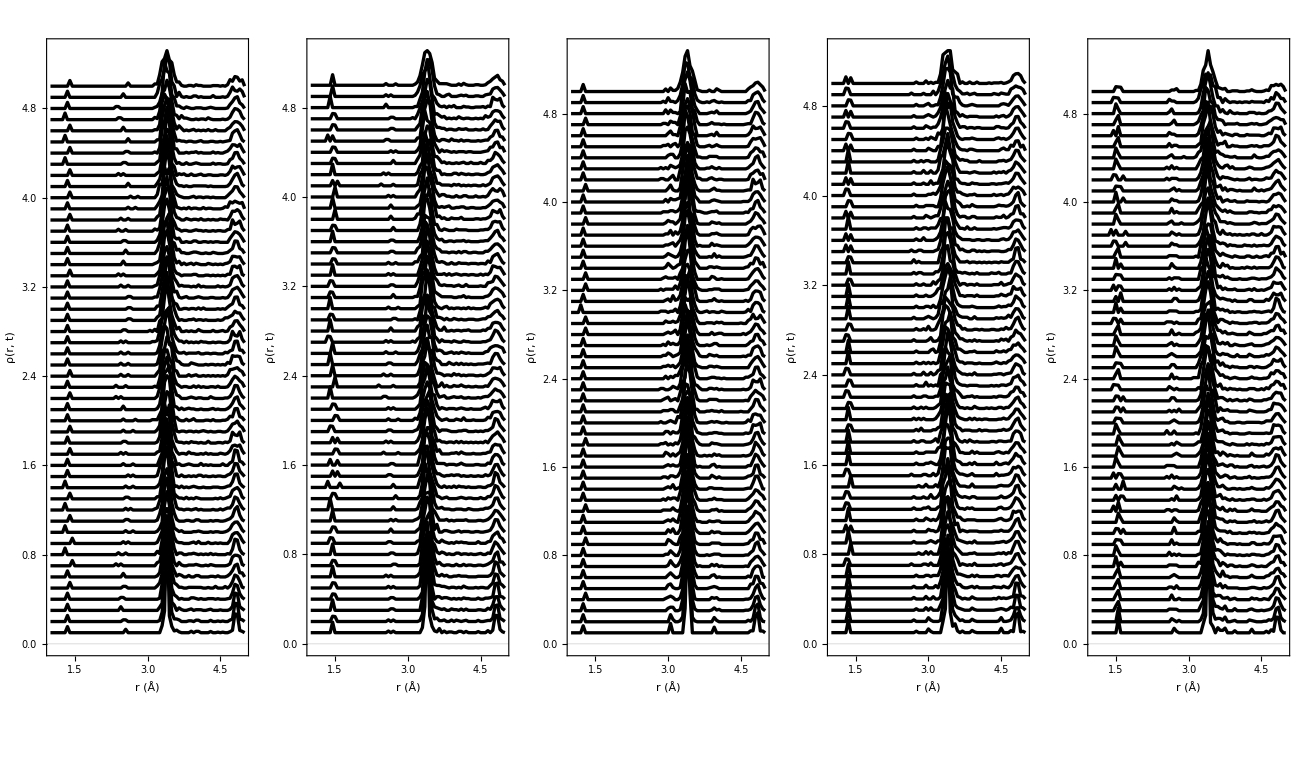

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[cc[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,50}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

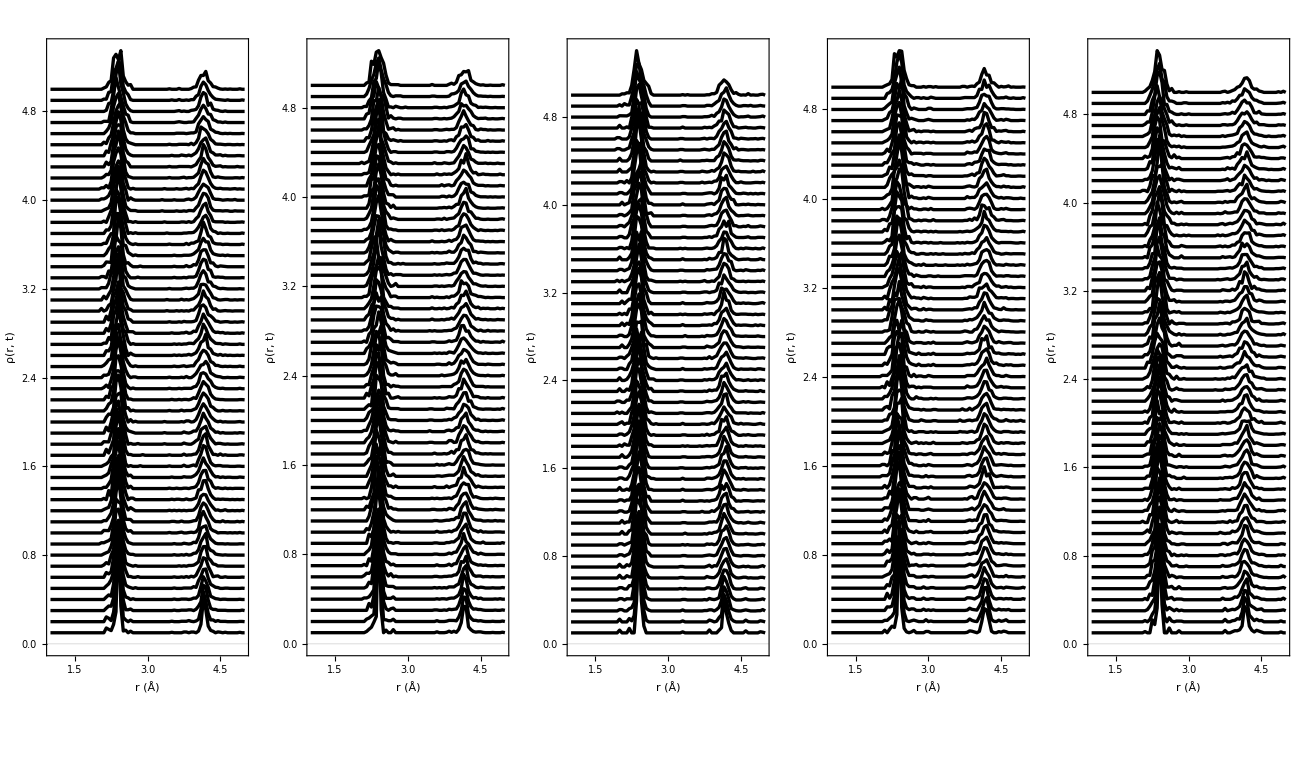

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[czr[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,50}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

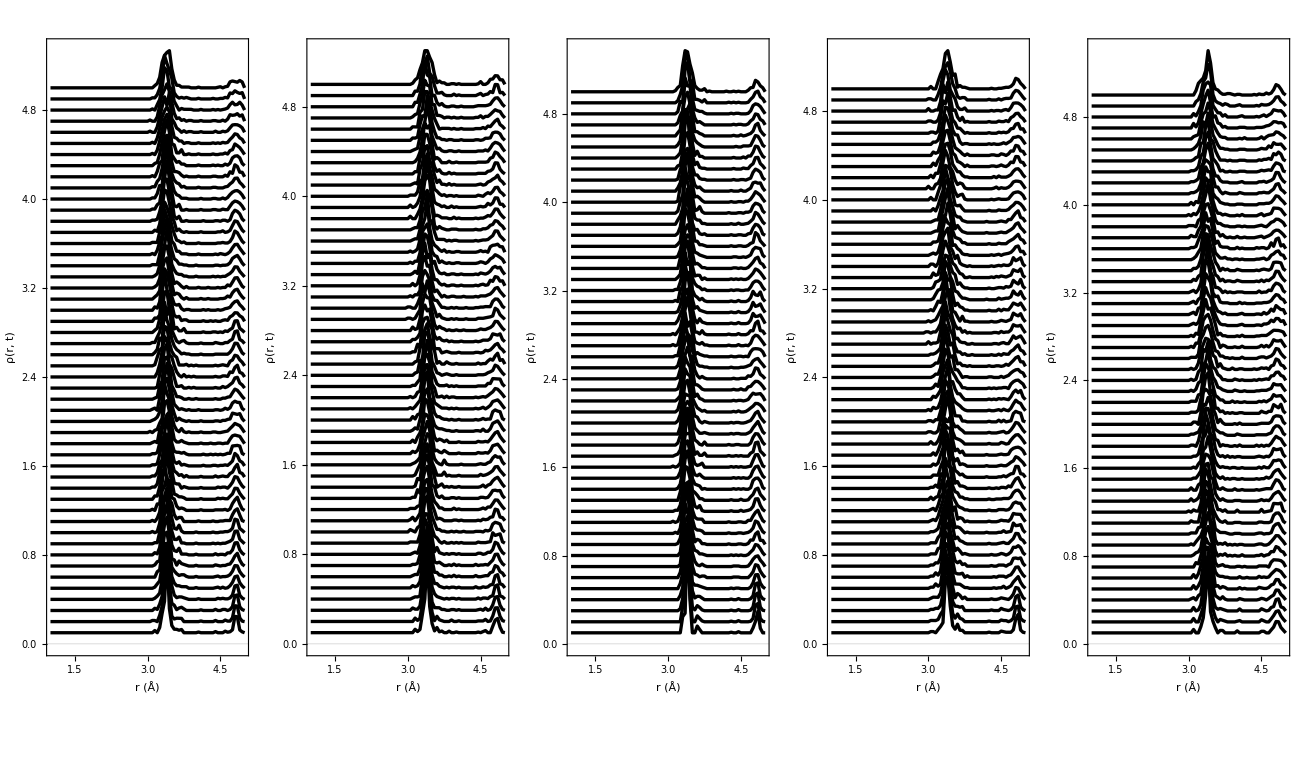

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[zrzr[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,50}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

## Production machine

Steps:
1) Import data at each temperature for each defect. 
2) Train a linear and SVMs on Initial 300K + 760K.
3) Train a bigger model on all temperatures

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results"];
(*Perfect*)
filesTestPerf={"pdf_OUT_perf.4850/m.pdf.PERF.4850.300.1_1071.txt","pdf_OUT_perf.4850/m.pdf.PERF.4850.760.1_186.txt","pdf_OUT_perf.4850/m.pdf.PERF.4850.1900.1_191.txt",
"pdf_OUT_perf.4850/m.pdf.PERF.4850.2500.1_166.txt","pdf_OUT_perf.4850/m.pdf.PERF.4850.3200.1_156.txt",
"pdf_OUT_perf.4850/m.pdf.PERF.4850.3805.1_151.txt"};
(*Bound*)
filesTest129={"pdf_OUT_129.4850/pdf.129.4850.300.1_1141.txt","pdf_OUT_129.4850/normal/m.pdf.129.4850.760.B2-01_129.txt","pdf_OUT_129.4850/normal/m.pdf.129.4850.1900.B2-01_108.txt",
"pdf_OUT_129.4850/normal/m.pdf.129.4850.2500.B2-01_45.txt","pdf_OUT_129.4850/normal/m.pdf.129.4850.3200.B2-01_30.txt",
"pdf_OUT_129.4850/normal/m.pdf.129.4850.3805.B2-01_28.txt"};
filesTest142={"pdf_OUT_142.4850/pdf.142.4850.300.1_891.txt","pdf_OUT_142.4850/normal/m.pdf.142.4850.760.B3-01_217.txt","pdf_OUT_142.4850/normal/m.pdf.142.4850.1900.B3-01_111.txt",
"pdf_OUT_142.4850/normal/m.pdf.142.4850.2500.B3-01_109.txt","pdf_OUT_142.4850/normal/m.pdf.142.4850.3200.B3-01_60.txt",
"pdf_OUT_142.4850/normal/m.pdf.142.4850.3805.B3-01_20.txt"};
(*Unbound*)
filesTest70={"pdf_OUT_70.4850/m.pdf.70.4850.300.1_842.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.760.U2-01_223.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.1900.U2-01_169.txt",
"pdf_OUT_70.4850/normal/m.pdf.70.4850.2500.U2-01_171.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.3200.U2-01_169.txt",
"pdf_OUT_70.4850/normal/m.pdf.70.4850.3805.U2-01_121.txt"};
filesTest174={"pdf_OUT_174.4850/pdf.174.4850.300.1_851.txt","pdf_OUT_174.4850/normal/m.pdf.174.4850.760.U3-01_171.txt","pdf_OUT_174.4850/normal/m.pdf.174.4850.1900.U3-01_197.txt",
"pdf_OUT_174.4850/normal/m.pdf.174.4850.2500.U3-01_166.txt","pdf_OUT_174.4850/normal/m.pdf.174.4850.3200.U3-01_81.txt",
"pdf_OUT_174.4850/normal/m.pdf.174.4850.3805.U3-01_158.txt"};

filesTest1126={"pdf_OUT_1126.4850/pdf.1126.4850.300.1_746.txt","pdf_OUT_1126.4850/normal/m.pdf.1126.4850.760.U4-01_176.txt","pdf_OUT_1126.4850/normal/m.pdf.1126.4850.1900.U4-01_69.txt",
"pdf_OUT_1126.4850/normal/m.pdf.1126.4850.2500.U4-01_67.txt","pdf_OUT_1126.4850/normal/m.pdf.1126.4850.3200.U4-01_54.txt",
"pdf_OUT_1126.4850/normal/m.pdf.1126.4850.760.U4-01_176.txt"};
filesDefectTypes={filesTest129,filesTest142,filesTest70,filesTest174,filesTest1126,filesTestPerf};
pdfDataProTest=Table[Table[ReadList[filesDefectTypes[[type]][[temp]],{Number,Number,Number,Number,Number}],{temp,1,Length@filesDefectTypes[[type]]}],{type,1,6}];
proSum={#[[1]],0.5*(#[[3]]+#[[4]])}&;
(*pdfDataProTest=Table[Table[ReadList[files[[j]][[i]],{Number,Number,Number,Number,Number}],{i,1,Length@files[[j]]}],{j,1,Length@files}]*)
```

```mathematica
pdfDataProTest[[defectType_]][[temperature_]]
```

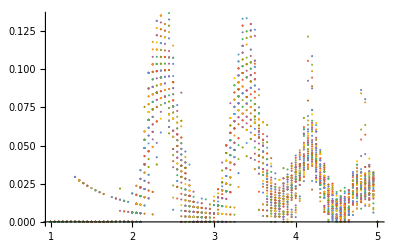

```mathematica
ListPlot@Table[Table[proSum/@Partition[pdfDataProTest[[1]][[j]],81][[i]],{i,1,Length@Partition[pdfDataProTest[[1]][[j]],81]}],{j,1,Length@pdfDataProTest[[1]]}][[4]]
```

### Bound Dimer

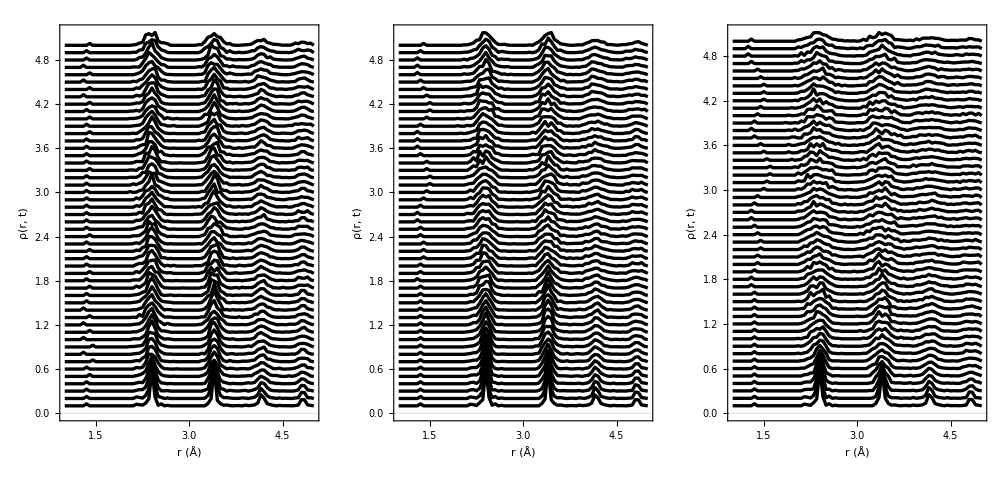

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum/@Partition[pdfDataProTest[[1]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[1]][[j]],81]}][[1;;50]],plotStyleA,AspectRatio->1.5],{j,1,6,2}]},ImageSize->1000,Spacings->2]
```

### Bound trimer

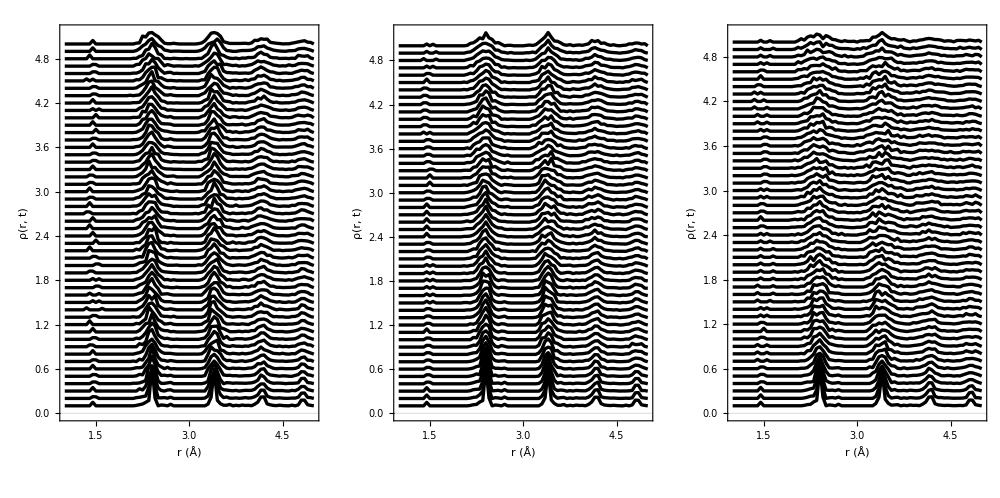

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum/@Partition[pdfDataProTest[[2]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[2]][[j]],81]}][[1;;50]],plotStyleA,AspectRatio->1.5],{j,1,3}]},ImageSize->1000,Spacings->2]
```

### Unbound dimer

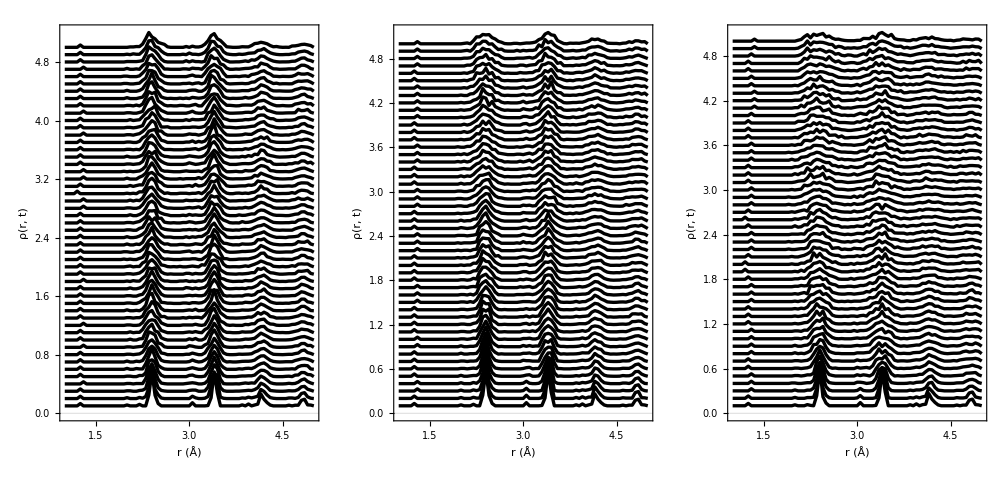

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum/@Partition[pdfDataProTest[[3]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[3]][[j]],81]}][[1;;50]],plotStyleA,AspectRatio->1.5],{j,1,3}]},ImageSize->1000,Spacings->2]
```

### Unbound trimer

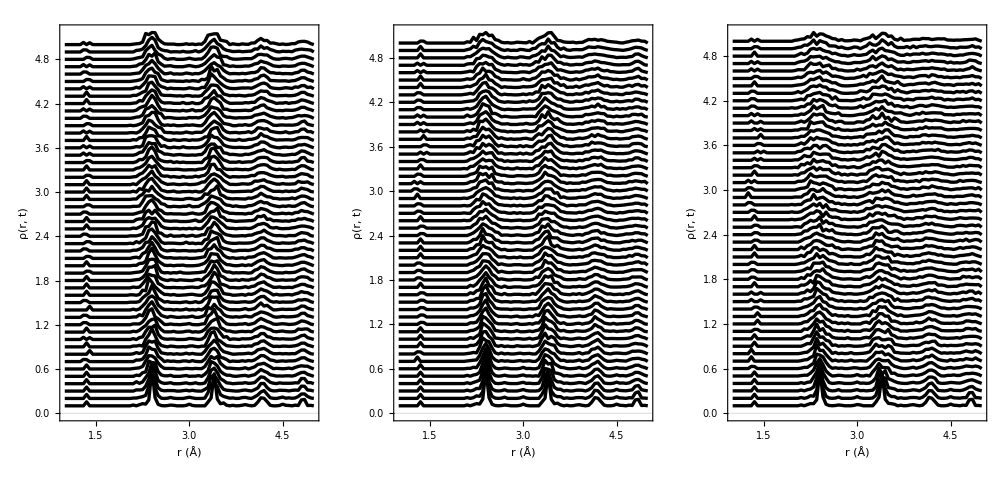

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum/@Partition[pdfDataProTest[[4]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[4]][[j]],81]}][[1;;50]],plotStyleA,AspectRatio->1.5],{j,1,3}]},ImageSize->1000,Spacings->2]
```

### Unbound tetramer

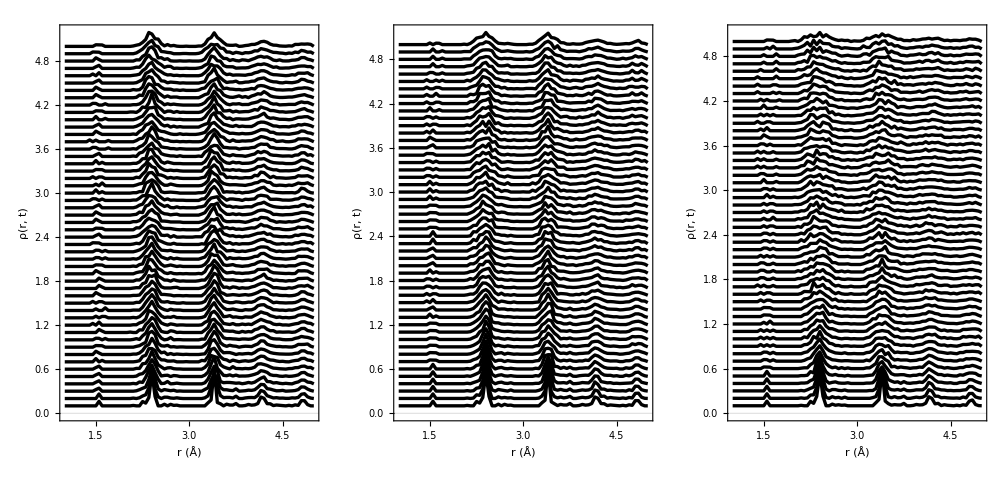

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum/@Partition[pdfDataProTest[[5]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[5]][[j]],81]}][[1;;50]],plotStyleA,AspectRatio->1.5],{j,1,3}]},ImageSize->1000,Spacings->2]
```

### 2-temperatures, 5-defects training

```mathematica
(*Model training*)
cSVM=With[{maxTypes=5,maxTemps=1,method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTemps}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
]
```

ClassifierFunction[…]

### 5-temps, 5 defects testing

```mathematica
(*Model testing*)
With[{maxTypes=5,maxTemps=5,method=methodsProduction[[2]],maxTempsTrain=1},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTemps}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTemps}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTemps}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTemps}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temps: ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
```

Model type: SupportVectorMachine, with training temps: {300}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200
Bound-dimer | 1. | 0.379845 | 0.12963 | 0.177778 | 0.2
Bound-trimer | 1. | 0.21659 | 0.0810811 | 0.0642202 | 0.1
Unbound-dimer | 1. | 0.2287 | 0.0769231 | 0.0408163 | 0.035503
Unbound-trimer | 1. | 0.426901 | 0.0659898 | 0.0361446 | 0.0617284
Unbound-tetramer | 1. | 1. | 1. | 1. | 1.

## Robustness of SVM classifier to new non-training temperatures -- transferability

### T=300K trained classifier

```mathematica
Module[{maxTempsTrain=1,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 0.395349 | 0.12963 | 0.177778 | 0.2 | 0.178571
Bound-trimer | 1. | 0.21659 | 0.0810811 | 0.0642202 | 0.1 | 0.25
Unbound-dimer | 1. | 0.264574 | 0.0828402 | 0.0408163 | 0.035503 | 0.0495868
Unbound-trimer | 1. | 0.444444 | 0.0659898 | 0.0421687 | 0.0617284 | 0.0316456
Unbound-tetramer | 1. | 1. | 1. | 1. | 1. | 1.
Perfect | 1. | 0.0263158 | 0. | 0. | 0.03125 | 0.0322581

### T={300K, 760K} trained classifier

```mathematica
Module[{maxTempsTrain=2,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 0.231481 | 0.4 | 0.5 | 0.464286
Bound-trimer | 1. | 1. | 0.27027 | 0.165138 | 0.233333 | 0.55
Unbound-dimer | 1. | 1. | 0.301775 | 0.158163 | 0.118343 | 0.14876
Unbound-trimer | 1. | 1. | 0.340102 | 0.144578 | 0.222222 | 0.0886076
Unbound-tetramer | 1. | 1. | 1. | 1. | 1. | 1.
Perfect | 1. | 1. | 0.0512821 | 0.0294118 | 0.03125 | 0.0322581

### T={300K,760K,1900K} trained classifier

```mathematica
Module[{maxTempsTrain=3,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760, 1900}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 1. | 0.844444 | 1. | 0.892857
Bound-trimer | 1. | 1. | 1. | 0.715596 | 0.75 | 0.8
Unbound-dimer | 1. | 1. | 1. | 0.964286 | 0.751479 | 0.586777
Unbound-trimer | 1. | 1. | 1. | 0.909639 | 0.851852 | 0.746835
Unbound-tetramer | 1. | 1. | 1. | 0.955224 | 0.851852 | 1.
Perfect | 1. | 1. | 1. | 1. | 1. | 0.709677

### T={300K, 760K, 1900K, 2500K} trained classifier

```mathematica
Module[{maxTempsTrain=4,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760, 1900, 2500}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 1. | 1. | 1. | 0.857143
Bound-trimer | 1. | 1. | 1. | 1. | 0.783333 | 0.9
Unbound-dimer | 1. | 1. | 1. | 1. | 0.940828 | 0.859504
Unbound-trimer | 1. | 1. | 1. | 1. | 0.91358 | 0.810127
Unbound-tetramer | 1. | 1. | 1. | 1. | 0.87037 | 1.
Perfect | 1. | 1. | 1. | 1. | 1. | 0.870968

### T={300K, 760K, 1900K, 2500K, 3200K} trained classifier

```mathematica
Module[{maxTempsTrain=5,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760, 1900, 2500, 3200}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 1. | 1. | 1. | 0.892857
Bound-trimer | 1. | 1. | 1. | 1. | 1. | 0.95
Unbound-dimer | 1. | 1. | 1. | 1. | 1. | 0.966942
Unbound-trimer | 1. | 1. | 1. | 1. | 1. | 0.71519
Unbound-tetramer | 1. | 1. | 1. | 1. | 1. | 1.
Perfect | 1. | 1. | 1. | 1. | 1. | 1.

### T={300K, 760K, 1900K, 2500K, 3200K, 3805K} trained classifier

```mathematica
Module[{maxTempsTrain=6,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760, 1900, 2500, 3200, 3805}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 1. | 1. | 1. | 1.
Bound-trimer | 1. | 1. | 1. | 1. | 1. | 1.
Unbound-dimer | 1. | 1. | 1. | 1. | 1. | 1.
Unbound-trimer | 1. | 1. | 1. | 1. | 1. | 1.
Unbound-tetramer | 1. | 1. | 1. | 1. | 1. | 1.
Perfect | 1. | 1. | 1. | 1. | 1. | 1.

## Visualise the classification space

{6,6}

{229,81,2}

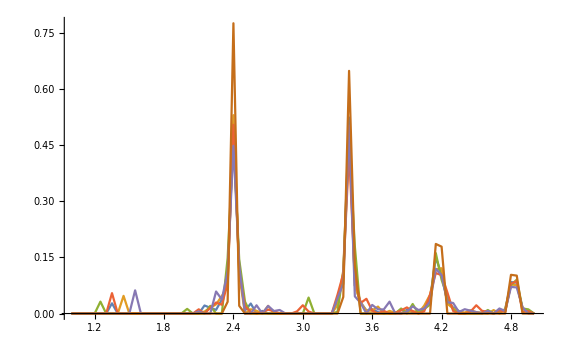

```mathematica
valData//Dimensions
valData[[1]][[1]]//Dimensions
typeExamples=Table[valData[[types]][[1]][[1]],{types,1,6}];
ListLinePlot[typeExamples,PlotRange->All]
```

```mathematica
Options@FeatureExtract
```

{PerformanceGoal→Automatic,NominalVariables→Automatic,FeatureNames→Automatic,FeatureTypes→Automatic,Weights→Automatic,FeatureWeights→Automatic,ProcessorCaching→False,OutputWrapper→Automatic,RecordLog→True}

```mathematica
feet=FeatureExtract[typeExamples]
xy=DimensionReduce[feet,2]
xyz=DimensionReduce[feet,3]
```

{{0.90131,-0.0408584,1.73969,-3.59014,3.85262},{2.00394,1.19871,0.115205,-4.53917,-3.33151},{-3.04614,-4.78463,-5.50597,0.227725,0.0946008},{1.89683,-4.49966,4.86153,2.98579,-0.83795},{6.04265,3.97145,-2.68995,3.30161,0.492337},{-7.79858,4.15499,1.47948,1.61418,-0.270092}}

{{-0.205802,0.0113773},{-0.457686,-0.33344},{0.696031,1.32973},{-0.433012,1.25172},{-1.38028,-1.10394},{1.78074,-1.15544}}

{{-0.205802,0.0113773,-0.522957},{-0.457686,-0.33344,-0.0346724},{0.696031,1.32973,1.65525},{-0.433012,1.25172,-1.46085},{-1.38028,-1.10394,0.808279},{1.78074,-1.15544,-0.445049}}

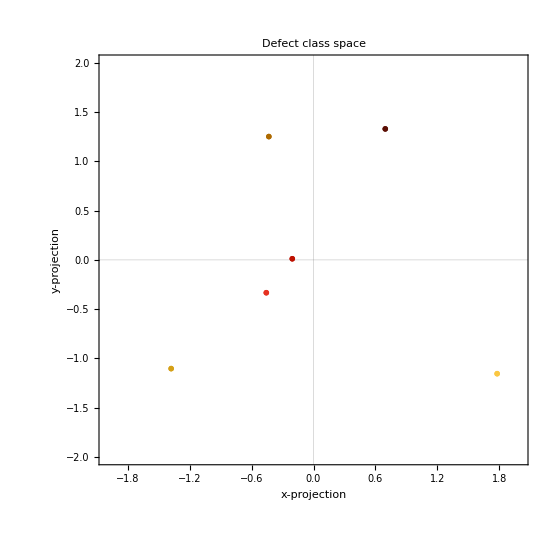

```mathematica
plotStyleC={AspectRatio->1,PlotRange->{{-2,2},{-2,2}},PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["x-projection",18,Black],Style["y-projection",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
bigName[a_]:=Style[a,24,FontFamily->Times]
bigName@fullNames;
ListPlot[List/@xy,PlotMarkers->(bigName/@fullNames),Frame->True,PlotStyle->20,plotStyleC,ImageSize->550,PlotLabel->Style["Defect class space",20,Black]]
```

```mathematica
plotStyleD={AxesStyle->Directive[Black, 22],AspectRatio->1,PlotRange->{{-2,2},{-2,2}},PlotTheme->"Scientific",Boxed->True,BoxStyle->Thickness[0.009],PlotStyle->Directive[Black,Thickness[0.06]],AxesLabel->{Style["x-projection",18,Black],Style["y-projection",18,Black],Style["z-projection",18,Black]}};
ListPointPlot3D[Table[{xyz[[i]]},{i,1,6}],AspectRatio->1,ImageSize->550,PlotStyle->PointSize[0.1],PlotLegends->fullNames,plotStyleD]
```

-Graphics3D-

```mathematica
xy1=Table[DimensionReduce[feet1[[i]],2],{i,1,5}]
xyz1=Table[DimensionReduce[feet1[[i]],3],{i,1,5}]
```

```mathematica
feet1=Table[FeatureExtract[Table[valData[[types]][[temps]][[1]],{types,1,6}]],{temps,1,5}];
feet1//Dimensions
xy1=Table[DimensionReduce[feet1[[i]],2],{i,1,5}];
xyz1=Table[DimensionReduce[feet1[[i]],3],{i,1,5}];
```

{5,6,5}

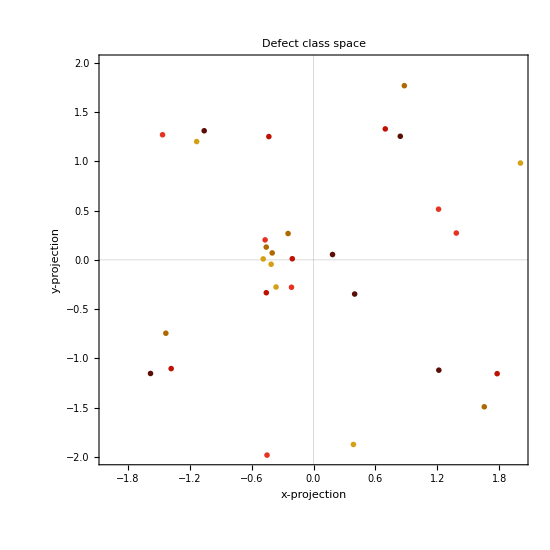

```mathematica
ListPlot[xy1,PlotMarkers->(bigName/@fullNames),Frame->True,PlotStyle->20,plotStyleC,ImageSize->550,PlotLabel->Style["Defect class space",20,Black]]
```

```mathematica
Show@Table[ListPointPlot3D[Table[{xyz1[[temp]][[i]]},{i,1,6}],AspectRatio->1,ImageSize->550,PlotStyle->PointSize[0.1],PlotLegends->fullNames,plotStyleD],{temp,1,5}]
```

-Graphics3D-

## Import Final Test Data

```mathematica
(*Bound*)
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_129.4850/normal/full_version"];
filesTestVal129={"m.pdf.129.4850.760.B2-01_129.B3-130_154.txt","m.pdf.129.4850.1900.B2-01_108.B3-109_179.txt","m.pdf.129.4850.2500.B2-01_45.B3-46-128.txt",
"m.pdf.129.4850.3200.B2-01_30.B3-30-137.txt"};
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_142.4850/normal/full_version"];
filesTestVal142={"m.pdf.142.4850.1900.B3-01_111.B4-112_156.B3-157_199.txt","m.pdf.142.4850.2500.B3-01_109.B4-110_124.B3-125_140.B2-141_142.B3-143_146.B2-147_157.B3-158_176.txt",
"m.pdf.142.4850.3200.B3-01_60.B2-61_64.B3-65_123.B4-124_133.B3-134_183.txt","m.pdf.142.4850.3805.B3-01_20.B2-21_114.B3-115_143.txt"};

(*Unbound*)
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_70.4850/normal/full_version"];
filesTestVal70={"m.pdf.70.4850.3200.U2-01_169.U3-170_185.txt","m.pdf.70.4850.3805.U2-01_121.U3-122_131.U4-132_143.U3-144_172.txt"};

SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_174.4850/normal/full_version"];
filesTestVal174={"m.pdf.174.4850.3200.U3-01_81.U2-82_92.U3-93_166.U2-167_170.U3-171_185.txt","m.pdf.174.4850.3805.U3-01_158.U4-159_181.txt"};

SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_1126.4850/normal/full_version"];
filesTestVal1126={"m.pdf.1126.4850.760.U4-01_176.U3-177-187.txt","m.pdf.1126.4850.1900.U4-01_69.U3-70_164.txt","m.pdf.1126.4850.2500.U4-01_67.U3-68_157.txt","m.pdf.1126.4850.3200.U4-01_54.U3-55_153.txt"};

filesDefectTypesVal={filesTestVal129,filesTestVal142,filesTestVal70,filesTestVal174,filesTestVal1126};
dirList={"/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_129.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_142.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_70.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_174.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_1126.4850/normal/full_version"};
```

```mathematica
pdfDataProTestVal=Table[Table[SetDirectory[dirList[[type]]];ReadList[filesDefectTypesVal[[type]][[temp]],{Number,Number,Number,Number,Number}],{temp,1,Length@filesDefectTypesVal[[type]]}],{type,1,5}];
```

```mathematica
proSum={#[[1]],0.5*(#[[3]]+#[[4]])}&;
proSum2={#[[1]],(#[[4]])}&;
CCdataSet=Table[Table[proSum2/@pdfDataProTestVal[[1]][[temp]],{temp,1,Length@filesDefectTypesVal[[type]]}],{type,1,5}]
```

{1}
 |  |  |  |

```mathematica
tList129={"760K","1900K","2500K","3200K"};
```

```mathematica
filesTestVal129
```

{m.pdf.129.4850.760.B2-01_129.B3-130_154.txt,m.pdf.129.4850.1900.B2-01_108.B3-109_159.B3-160_173.B3-174_179.txt,m.pdf.129.4850.2500.B2-01_45.B3-46-128.txt,m.pdf.129.4850.3200.B2-01_30.B3-30-137.txt}

```mathematica
ListproSum2/@Partition[pdfDataProTestVal[[1]][[1]],81][[1]]/.{a_,b_}:>{a,b+1/15};
```

```mathematica
filesTestVal129[[;;]]
```

{m.pdf.129.4850.760.B2-01_129.B3-130_154.txt,m.pdf.129.4850.1900.B2-01_108.B3-109_159.B3-160_173.B3-174_179.txt,m.pdf.129.4850.2500.B2-01_45.B3-46-128.txt,m.pdf.129.4850.3200.B2-01_30.B3-30-137.txt}

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum2/@Partition[pdfDataProTestVal[[1]][[temp]],81][[timeStep]]/.{a_,b_}:>{a,15*b+timeStep},{timeStep,1,Length@Partition[pdfDataProTestVal[[1]][[temp]],81]}][[]],plotStyleA,AspectRatio->2,PlotLabel->Style[filesTestVal129[[temp]],14,Black]],{temp,1,filesTestVal129[[;;]]//Length}]},ImageSize->1500,Spacings->2]
```

-Graphics-

### Compute mean pdfs

```mathematica
Partition[pdfDataProTest[[2]][[1]],81]//Length
```

179

```mathematica
ListLinePlot[Table[Table[Mean@Table[proSum2/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,6}],{type,6,6}][[1]],PlotRange->All,PlotLegends->temperatures,PlotStyle->Thickness[0.006]]
```

-Graphics-

```mathematica
data=Table[Table[Mean@Table[proSum2/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,6}],{type,6,6}][[1]][[1]]
```

{{1.,0.},{1.05,0.},{1.1,0.},{1.15,0.},{1.2,0.},{1.25,0.},{1.3,0.},{1.35,0.},{1.4,0.},{1.45,0.},{1.5,0.},{1.55,0.},{1.6,0.},{1.65,0.},{1.7,0.},{1.75,0.},{1.8,0.},{1.85,0.},{1.9,0.},{1.95,0.},{2.,0.},{2.05,0.},{2.1,0.},{2.15,0.},{2.2,0.},{2.25,0.},{2.3,0.},{2.35,0.},{2.4,0.},{2.45,0.},{2.5,0.},{2.55,0.},{2.6,0.},{2.65,0.},{2.7,0.},{2.75,0.},{2.8,0.},{2.85,0.},{2.9,0.},{2.95,0.},{3.,0.},{3.05,0.},{3.1,0.000386977},{3.15,0.00232558},{3.2,0.0134516},{3.25,0.0594856},{3.3,0.179936},{3.35,0.33418},{3.4,0.424518},{3.45,0.353253},{3.5,0.189179},{3.55,0.0697512},{3.6,0.0185395},{3.65,0.00302884},{3.7,0.000509302},{3.75,0.},{3.8,0.},{3.85,0.},{3.9,0.},{3.95,0.},{4.,0.},{4.05,0.},{4.1,0.},{4.15,0.},{4.2,0.},{4.25,0.},{4.3,0.},{4.35,0.},{4.4,0.},{4.45,0.},{4.5,0.},{4.55,0.000156279},{4.6,0.00144279},{4.65,0.00810884},{4.7,0.0290302},{4.75,0.0661847},{4.8,0.102636},{4.85,0.101506},{4.9,0.0643209},{4.95,0.0278363},{5.,0.}}

```mathematica
fInt=Interpolation[data]
```

InterpolatingFunction[{{1., 5.}}, <>]

```mathematica
Plot[fInt[x],{x,0,5},PlotRange->All]
max=FindMaximum[fInt[x],{x,3.5}][[1]]/2
NSolve[fInt[x]==max,x]//Reduce
```

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.212259

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

Reduce::naqs: {x→InverseFunction[«1»,1,1][0.212259]} is not a quantified system of equations and inequalities.

Reduce[{{x→InverseFunction[InterpolatingFunction[{{1., 5.}}, <>],1,1][0.212259]}}]

```mathematica
model=Sum[(parameterListThrees[[counter]][[3]]*PDF[CauchyDistribution[parameterListThrees[[counter]][[1]],parameterListThrees[[counter]][[2]]],x]),{counter,1,Length@parameterListThrees}];

model[x_]=model+correction
nonlinFitA=NonlinearModelFit[zircPeakA,model,parameterList,x,MaxIterations->10000]
```

Set::write: Tag Integer in 0[x_] is Protected.

correction

NonlinearModelFit::fitd: First argument zircPeakA in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[zircPeakA,0,parameterList,x,MaxIterations→10000]

```mathematica
data2=Table[{x,fInt[x]},{x,3,4,0.001}];
data3=Table[{x,fInt[x]},{x,4,5,0.001}];
```

```mathematica
nonlinFitA=NonlinearModelFit[data2,c*PDF[NormalDistribution[a,b],x],{a,b,c},x]
nonlinFitB=NonlinearModelFit[data3,h*PDF[NormalDistribution[f,g],x],{f,g,h},x]
nonLinFit=nonlinFitA+nonlinFitB
```

FittedModel[0.421901 ⅇ^(-82.2475 («1»)^2)]

FittedModel[0.107145 ⅇ^(-86.6382 («1»)^2)]

FittedModel[0.421901 ⅇ^(-82.2475 («1»)^2)]+FittedModel[0.107145 ⅇ^(-86.6382 («1»)^2)]

```mathematica
Plot[nonlinFitB,{x,0,5},PlotRange->All]
```

-Graphics-

```mathematica
fInt
```

InterpolatingFunction[{{1., 5.}}, <>]

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/"];
filesTest70={"pdf_OUT_70.4850/normal/m.pdf.70.4850.760.U2-01_223.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.1900.U2-01_169.txt",
"pdf_OUT_70.4850/normal/m.pdf.70.4850.2500.U2-01_171.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.3200.U2-01_169.txt",
"pdf_OUT_70.4850/normal/m.pdf.70.4850.3805.U2-01_121.txt"};
pdfDataTest=Table[ReadList[filesTest70[[i]],{Number,Number,Number,Number,Number}],{i,1,Length@filesTest70}];


zrzrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[2]]},{i,1,5}];
czrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[3]]},{i,1,5}];
ccTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[4]]},{i,1,5}];
totTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[5]]},{i,1,5}];
```

```mathematica
Table[Partition[pdfDataTest[[i]],81]//Length,{i,1,Length@pdfDataTest}]
```

{223,169,196,169,121}

#### PDF plot, animation, and export;

```mathematica
ListLinePlot[Partition[ccTest[[5]],81][[]],plotStyle]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[ccTest[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,120}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[zrzrTest[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,120}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[czrTest[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,120}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

-Graphics-

```mathematica
(*ccTestAnimation=Table[With[{name=ccTest},ListAnimate[Table[ListLinePlot[Partition[name[[j]],81][[i]],plotStyle,PlotLabel->Style[volumes[[j]],18,Black]],{i,1,Partition[name[[j]],81]//Length}],25]],{j,1,2}]*)
```

```mathematica
(*SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/animations"];
framesTestingCC=Table[With[{name=ccTest},Table[ListLinePlot[Partition[name[[j]],81][[i]],Frame->True,plotStyle,PlotLabel->Style["3000 K MD",18,Black]],{i,1,Partition[name[[j]],81]//Length}]],{j,1,1}];
framesTestingCCJoined=Join[framesTestingCC[[1]],framesTestingCC[[1]]];
Export["framesTestingCC.gif",framesTestingCCJoined,"AnimationRepetitions"->1,"ControlAppearance"->None]*)
```